```mathematica
Genus Two Minesweeper
```

By: Kaaustaaub Shankar and Matthew Pimienta
An actual implementation of double torus Minesweeper which we will use to perform queries for the solver.

### Play

```mathematica
(*Evaluate all the cells and run the segment below to run the game
If you wish to use the randomize button and sliders under them, make sure that the mineDensity * 8*numOfRows^2 is an integer*)
sector = 1;
row = 1;
column = 1;
numOfRows = 10;
mineDensity = 0.25;
flag = Floor[8*mineDensity*numOfRows*numOfRows];
board=boardSetUp[numOfRows,flag,{sector,row,column}];
type = "Reveal";
count = 0;
boardGraphics = displayBoard[board];
sectionLst = {};
play[board,boardGraphics]
```

Flags Left: 
Revealed Tiles: 

Randomize
{,Rows: }
{,Mine Density: }
{,Sector Clicked: }
{,Row Clicked: }
{,Tile Clicked: }

### Using the Solver

```mathematica
solverInterface=initSolver[numOfRows];
```

```mathematica
(*One step of the solver*)
Print["Before"];
Graphics[displayBoard[board]]
interfaceNext[solverInterface,testHeur,True];
Print["After"];
Graphics[displayBoard[board]]
```

```mathematica
(*Run the code to activate the solver*)
progression = autoSolve[solverInterface,testHeur];
```

Step 1

Step 2

Step 3

Step 4

Step 5

Step 6

Step 7

Step 8

Step 9

Step 10

Step 11

Step 12

Step 13

Step 14

Step 15

Step 16

Step 17

Step 18

Step 19

Step 20

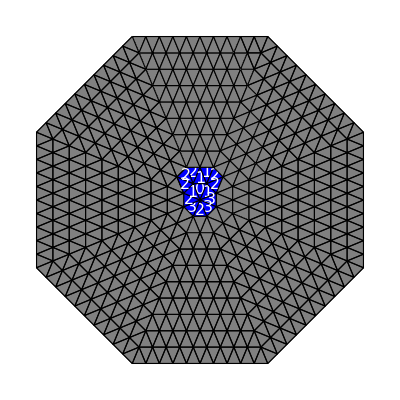
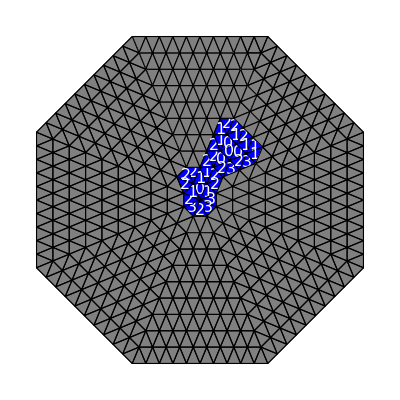
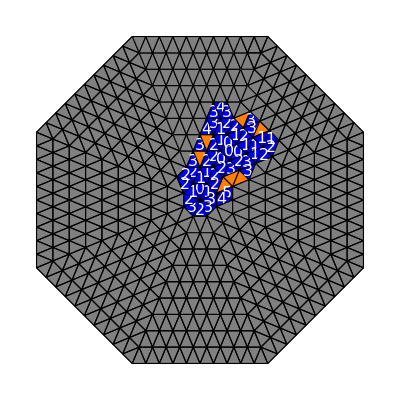
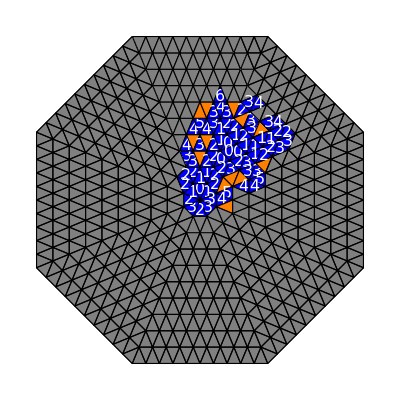
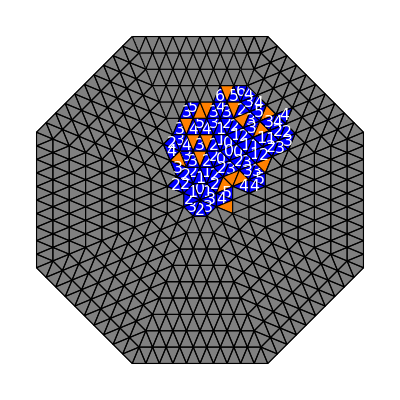
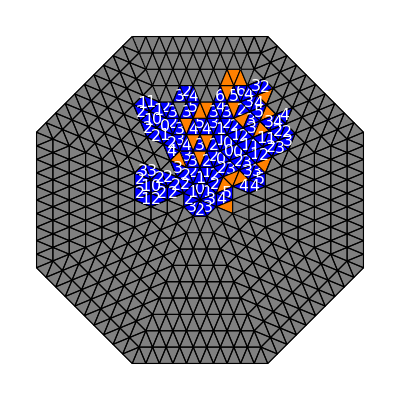
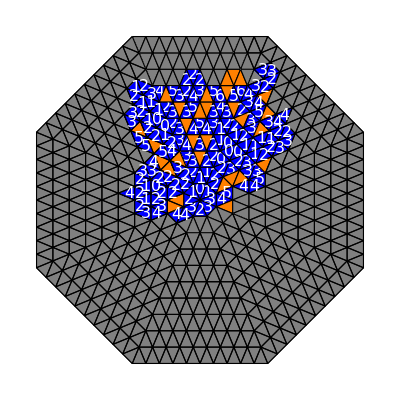
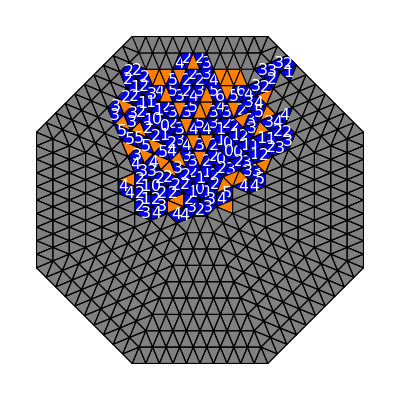

```mathematica
{Graphics@boardGraphics,Flatten[Table[Graphics@progression⟦i⟧,{i,1,Length@progression - 1}],1]}
```

### Setting Up Board

#### Global variables

Indexing

```mathematica
MINETYPEI=1;
REVEALORNOT = 2;
NEIGHBORDATAI=3;
TRIPOINTI=4;
NMINESI=5;
ISFLAGGEDI = 6;
```

Mine and other attributes

```mathematica
MINE = 1;
NOTMINE = 0;
NOTREVEALED = 0;
REVEALED = 1;
ISFLAGGED = True;
NOTFLAGGED = False;
```

#### Getters

```mathematica
getTileType[board_,sector_,row_,column_]:=board⟦sector,row,column,1⟧
```

```mathematica
getTilePoints[board_,sector_,row_,column_]:=board⟦sector,row,column,2⟧
```

```mathematica
getNeighborPos[board_,sector_,row_,column_]:=board⟦sector,row,column,3⟧
```

```mathematica
(*Returns tile data for structured board*)
getTile[board_,listPos_]:=board⟦listPos⟦1⟧,listPos⟦2⟧,listPos⟦3⟧⟧
```

```mathematica
isComplete[board_]:=
Module[
{},
Do[
If[tile⟦REVEALORNOT⟧==NOTREVEALED&&tile⟦MINETYPEI⟧==NOTMINE,Return[False]]
,{sector,board}
,{row,sector}
,{tile,row}
];
Return[True]
]
```

#### Mine setup

```mathematica
neighborsWith0[board_, section_,row_,column_]:=Select[board⟦section,row,column,3⟧,board⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,1⟧===0&&board⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,2⟧===0 &]
```

```mathematica
(*This method returns a board without the primitives, just if its a mine or not*)
setupMines[numOfRows_,factor_]:= 
Module[
{tiles = 8*numOfRows^2 ,
lst = Table[{},{x,1,8}],
row,section,
numOfTiles,remainingMineCount,tile,skeletons,neighbors},

remainingMineCount = factor * tiles;
(*For loop for stacking *)
For[row = 1,row≤ numOfRows,row++,
(*Goes through each section*)
For[section = 1, section≤ 8, section++,
AppendTo[lst⟦section⟧,{}];
(*Loop to add tiles to each section & row*)
For[numOfTiles= 1, numOfTiles≤ 2*row - 1,numOfTiles++,
(*zeros are  not mines and 1s are mines*)
tile = RandomChoice[{remainingMineCount/tiles,(tiles - remainingMineCount)/tiles}->{MINE,NOTMINE}];
If[tile===MINE,
remainingMineCount--;
];
tiles--;
AppendTo[lst⟦section⟧⟦row⟧,tile]
]
]
];

Return [lst]
]
```

```mathematica
setupMines[3,0.25]
```

{{{{0,0}},{{0,0},{0,0},{0,0}},{{0,0},{1,0},{0,0},{1,0},{0,0}}},{{{0,0}},{{0,0},{0,0},{1,0}},{{1,0},{0,0},{0,0},{0,0},{0,0}}},{{{0,0}},{{0,0},{1,0},{0,0}},{{1,0},{0,0},{0,0},{0,0},{1,0}}},{{{1,0}},{{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0}}},{{{0,0}},{{0,0},{0,0},{0,0}},{{1,0},{1,0},{0,0},{0,0},{0,0}}},{{{0,0}},{{0,0},{0,0},{0,0}},{{0,0},{0,0},{1,0},{0,0},{0,0}}},{{{1,0}},{{1,0},{1,0},{1,0}},{{0,0},{0,0},{0,0},{1,0},{0,0}}},{{{0,0}},{{1,0},{1,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0}}}}

```mathematica
(*This method returns a board without the primitives, just if its a mine or not*)
setupMines[numOfRows_,numMines_,offLimits_]:= 
Module[
{indicesPlace=RandomSample[Table[If[!MemberQ[offLimits,boardifyFlatIndex[i,numOfRows]],i,Nothing],{i,8 numOfRows^2}],numMines],
currentIndex,
mineLst=Table[NOTMINE,{sector,8},{row,numOfRows},{tile,2row-1}]
},

Do[
currentIndex=boardifyFlatIndex[index,numOfRows];
mineLst⟦currentIndex⟦1⟧,currentIndex⟦2⟧,currentIndex⟦3⟧⟧=MINE;
,{index,indicesPlace}
];

Return [mineLst]
]
```

```mathematica
Table[0,{x,8},{y,8},{z,8}]
```

{{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}}

#### Triangle point setup

Setting up coordinates of triangles.

```mathematica
(*Construct a single row of triangles for the tiling*)
constructTiledTriangleRow[numItems_,offset_]:=Module[
{(*This constructs the zigzag shape of the triangles*)
zigzag=Riffle[
Table[N@{pointX,Sin[(3π)/8]}+offset,{pointX,-(numItems+1)/2 Cos[(3π)/8],(numItems+1)/2 Cos[(3π)/8],2Cos[(3π)/8]}],
Table[N@{pointX,0}+offset,{pointX,-(numItems-1)/2 Cos[(3π)/8],(numItems-1)/2 Cos[(3π)/8],2Cos[(3π)/8]}]

]
},
(*Take advantage of the zigzag shape to construct triangles*)
Return[Table[{zigzag⟦i⟧,zigzag⟦i+1⟧,zigzag⟦i+2⟧},{i,numItems}]]
]
```

```mathematica
constructTiledTriangleRow[5,{0,0}]
```

{{{-1.14805,0.92388},{-0.765367,0.},{-0.382683,0.92388}},{{-0.765367,0.},{-0.382683,0.92388},{0.,0.}},{{-0.382683,0.92388},{0.,0.},{0.382683,0.92388}},{{0.,0.},{0.382683,0.92388},{0.765367,0.}},{{0.382683,0.92388},{0.765367,0.},{1.14805,0.92388}}}

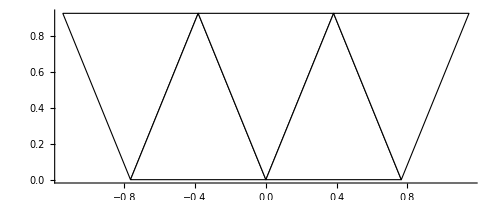

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[constructTiledTriangleRow[5,{0,0}]]},Axes->True]
```

```mathematica
(*Constructs a "big" triangle*)
constructTiledTriangle[numRows_]:=Table[constructTiledTriangleRow[numTriangles,{0,(numTriangles-1)/2*Sin[(3π)/8]}],{numTriangles,1,2numRows-1,2}]
```

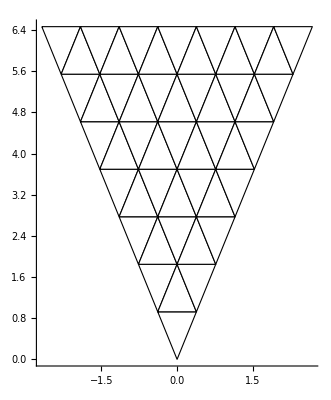

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@constructTiledTriangle[7]]},Axes->True]
```

```mathematica
(*Rotate points of a triangle created from constructTiledTriangle*)
rotateMassTriangle[triangles_,θ_]:=Table[Table[Table[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.point,{point,triangle}],{triangle,row}],{row,triangles}]
```

```mathematica
(*Construct triangle points for the board tiles.
The return structure is structured the same way as a regular board, except this only gives tile corner coordinates
*)
createBoardSkeleton[numRows_]:=Table[rotateMassTriangle[constructTiledTriangle[numRows],θ],{θ,2π,π/4,-π/4}]
```

```mathematica
createBoardSkeleton[3]
```

{{{{{-0.382683,0.92388},{0.,0.},{0.382683,0.92388}}},{{{-0.765367,1.84776},{-0.382683,0.92388},{0.,1.84776}},{{-0.382683,0.92388},{0.,1.84776},{0.382683,0.92388}},{{0.,1.84776},{0.382683,0.92388},{0.765367,1.84776}}},{{{-1.14805,2.77164},{-0.765367,1.84776},{-0.382683,2.77164}},{{-0.765367,1.84776},{-0.382683,2.77164},{0.,1.84776}},{{-0.382683,2.77164},{0.,1.84776},{0.382683,2.77164}},{{0.,1.84776},{0.382683,2.77164},{0.765367,1.84776}},{{0.382683,2.77164},{0.765367,1.84776},{1.14805,2.77164}}}},{{{{0.382683,0.92388},{0.,0.},{0.92388,0.382683}}},{{{0.765367,1.84776},{0.382683,0.92388},{1.30656,1.30656}},{{0.382683,0.92388},{1.30656,1.30656},{0.92388,0.382683}},{{1.30656,1.30656},{0.92388,0.382683},{1.84776,0.765367}}},{{{1.14805,2.77164},{0.765367,1.84776},{1.68925,2.23044}},{{0.765367,1.84776},{1.68925,2.23044},{1.30656,1.30656}},{{1.68925,2.23044},{1.30656,1.30656},{2.23044,1.68925}},{{1.30656,1.30656},{2.23044,1.68925},{1.84776,0.765367}},{{2.23044,1.68925},{1.84776,0.765367},{2.77164,1.14805}}}},{{{{0.92388,0.382683},{0.,0.},{0.92388,-0.382683}}},{{{1.84776,0.765367},{0.92388,0.382683},{1.84776,0.}},{{0.92388,0.382683},{1.84776,0.},{0.92388,-0.382683}},{{1.84776,0.},{0.92388,-0.382683},{1.84776,-0.765367}}},{{{2.77164,1.14805},{1.84776,0.765367},{2.77164,0.382683}},{{1.84776,0.765367},{2.77164,0.382683},{1.84776,0.}},{{2.77164,0.382683},{1.84776,0.},{2.77164,-0.382683}},{{1.84776,0.},{2.77164,-0.382683},{1.84776,-0.765367}},{{2.77164,-0.382683},{1.84776,-0.765367},{2.77164,-1.14805}}}},{{{{0.92388,-0.382683},{0.,0.},{0.382683,-0.92388}}},{{{1.84776,-0.765367},{0.92388,-0.382683},{1.30656,-1.30656}},{{0.92388,-0.382683},{1.30656,-1.30656},{0.382683,-0.92388}},{{1.30656,-1.30656},{0.382683,-0.92388},{0.765367,-1.84776}}},{{{2.77164,-1.14805},{1.84776,-0.765367},{2.23044,-1.68925}},{{1.84776,-0.765367},{2.23044,-1.68925},{1.30656,-1.30656}},{{2.23044,-1.68925},{1.30656,-1.30656},{1.68925,-2.23044}},{{1.30656,-1.30656},{1.68925,-2.23044},{0.765367,-1.84776}},{{1.68925,-2.23044},{0.765367,-1.84776},{1.14805,-2.77164}}}},{{{{0.382683,-0.92388},{0.,0.},{-0.382683,-0.92388}}},{{{0.765367,-1.84776},{0.382683,-0.92388},{0.,-1.84776}},{{0.382683,-0.92388},{0.,-1.84776},{-0.382683,-0.92388}},{{0.,-1.84776},{-0.382683,-0.92388},{-0.765367,-1.84776}}},{{{1.14805,-2.77164},{0.765367,-1.84776},{0.382683,-2.77164}},{{0.765367,-1.84776},{0.382683,-2.77164},{0.,-1.84776}},{{0.382683,-2.77164},{0.,-1.84776},{-0.382683,-2.77164}},{{0.,-1.84776},{-0.382683,-2.77164},{-0.765367,-1.84776}},{{-0.382683,-2.77164},{-0.765367,-1.84776},{-1.14805,-2.77164}}}},{{{{-0.382683,-0.92388},{0.,0.},{-0.92388,-0.382683}}},{{{-0.765367,-1.84776},{-0.382683,-0.92388},{-1.30656,-1.30656}},{{-0.382683,-0.92388},{-1.30656,-1.30656},{-0.92388,-0.382683}},{{-1.30656,-1.30656},{-0.92388,-0.382683},{-1.84776,-0.765367}}},{{{-1.14805,-2.77164},{-0.765367,-1.84776},{-1.68925,-2.23044}},{{-0.765367,-1.84776},{-1.68925,-2.23044},{-1.30656,-1.30656}},{{-1.68925,-2.23044},{-1.30656,-1.30656},{-2.23044,-1.68925}},{{-1.30656,-1.30656},{-2.23044,-1.68925},{-1.84776,-0.765367}},{{-2.23044,-1.68925},{-1.84776,-0.765367},{-2.77164,-1.14805}}}},{{{{-0.92388,-0.382683},{0.,0.},{-0.92388,0.382683}}},{{{-1.84776,-0.765367},{-0.92388,-0.382683},{-1.84776,0.}},{{-0.92388,-0.382683},{-1.84776,0.},{-0.92388,0.382683}},{{-1.84776,0.},{-0.92388,0.382683},{-1.84776,0.765367}}},{{{-2.77164,-1.14805},{-1.84776,-0.765367},{-2.77164,-0.382683}},{{-1.84776,-0.765367},{-2.77164,-0.382683},{-1.84776,0.}},{{-2.77164,-0.382683},{-1.84776,0.},{-2.77164,0.382683}},{{-1.84776,0.},{-2.77164,0.382683},{-1.84776,0.765367}},{{-2.77164,0.382683},{-1.84776,0.765367},{-2.77164,1.14805}}}},{{{{-0.92388,0.382683},{0.,0.},{-0.382683,0.92388}}},{{{-1.84776,0.765367},{-0.92388,0.382683},{-1.30656,1.30656}},{{-0.92388,0.382683},{-1.30656,1.30656},{-0.382683,0.92388}},{{-1.30656,1.30656},{-0.382683,0.92388},{-0.765367,1.84776}}},{{{-2.77164,1.14805},{-1.84776,0.765367},{-2.23044,1.68925}},{{-1.84776,0.765367},{-2.23044,1.68925},{-1.30656,1.30656}},{{-2.23044,1.68925},{-1.30656,1.30656},{-1.68925,2.23044}},{{-1.30656,1.30656},{-1.68925,2.23044},{-0.765367,1.84776}},{{-1.68925,2.23044},{-0.765367,1.84776},{-1.14805,2.77164}}}}}

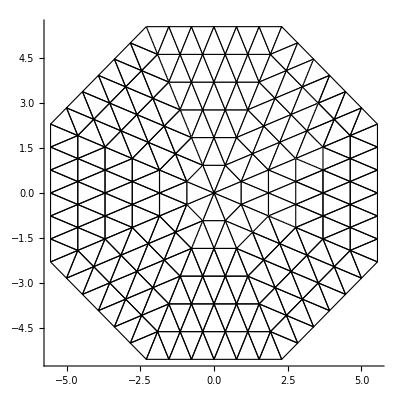

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@Join@@createBoardSkeleton[6]]},Axes->True]
```

#### Neighbors setup (point comparison)

We use an association to figure out which triangles share points. The coordinates will be rounded by a 1/100 to accommodate a reasonable floating point error.
We then handle adjacencies by outer edge connection as a separate case

```mathematica
(*Error checking to ensure we do not add any invalid neighbors. Less cases to handle manually*)
SetAttributes[addNeighbor,HoldFirst]
addNeighbor[neighborLst_,numRows_,sector_,row_,tile_]:=
If[1≤sector≤8&&1≤row≤numRows&&1≤tile≤2*row-1&&!MemberQ[neighborLst,{sector,row,tile}],AppendTo[neighborLst,{sector,row,tile}]
]
```

```mathematica
roundCoordHundredths[coord_]:=Map[Round[#*100]/100.&,coord]
```

```mathematica
(*Returns an association. Each key is a point rounded to the hundredths, and the values are lists of triangles which have that point*)
findSharedPoints[trianglesCoords_]:=
Module[{pointsAssociations=Association[]},

Do[
(*Point is not yet in association*)
If[MissingQ@pointsAssociations[roundCoordHundredths[point]],
AssociateTo[pointsAssociations,roundCoordHundredths[point]->{}];
];
(*Add point to association*)
AssociateTo[pointsAssociations,roundCoordHundredths[point]->Append[pointsAssociations[roundCoordHundredths[point]],{sectorI,rowI,tileI}]];
,{sectorI,Length@trianglesCoords}
,{rowI,Length@trianglesCoords⟦sectorI⟧}
,{tileI,Length@trianglesCoords⟦sectorI,rowI⟧}
,{point,trianglesCoords⟦sectorI,rowI,tileI⟧}
];
Return[pointsAssociations]
]
```

```mathematica
Length@createBoardSkeleton[3]⟦1⟧
```

3

```mathematica
findSharedPoints[createBoardSkeleton[2]]
```

<|{-0.38,0.92}→{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3}},{0.,0.}→{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1}},{0.38,0.92}→{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,1},{2,2,2}},{-0.77,1.85}→{{1,2,1},{8,2,3}},{0.,1.85}→{{1,2,1},{1,2,2},{1,2,3}},{0.77,1.85}→{{1,2,3},{2,2,1}},{0.92,0.38}→{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,1},{3,2,2}},{1.31,1.31}→{{2,2,1},{2,2,2},{2,2,3}},{1.85,0.77}→{{2,2,3},{3,2,1}},{0.92,-0.38}→{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,1},{4,2,2}},{1.85,0.}→{{3,2,1},{3,2,2},{3,2,3}},{1.85,-0.77}→{{3,2,3},{4,2,1}},{0.38,-0.92}→{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,1},{5,2,2}},{1.31,-1.31}→{{4,2,1},{4,2,2},{4,2,3}},{0.77,-1.85}→{{4,2,3},{5,2,1}},{-0.38,-0.92}→{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,1},{6,2,2}},{0.,-1.85}→{{5,2,1},{5,2,2},{5,2,3}},{-0.77,-1.85}→{{5,2,3},{6,2,1}},{-0.92,-0.38}→{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,1},{7,2,2}},{-1.31,-1.31}→{{6,2,1},{6,2,2},{6,2,3}},{-1.85,-0.77}→{{6,2,3},{7,2,1}},{-0.92,0.38}→{{7,1,1},{7,2,2},{7,2,3},{8,1,1},{8,2,1},{8,2,2}},{-1.85,0.}→{{7,2,1},{7,2,2},{7,2,3}},{-1.85,0.77}→{{7,2,3},{8,2,1}},{-1.31,1.31}→{{8,2,1},{8,2,2},{8,2,3}}|>

```mathematica
countMines[mineLst_,neighborLst_,sector_,row_,tile_]:=Module[
{},
Return[Length@Select[neighborLst⟦sector,row,tile,1⟧,mineLst⟦#⟦1⟧,#⟦2⟧,#⟦3⟧⟧==1&]]
]
```

```mathematica
(*Returns the neighbors of each tile in the tiling given the coordinates of the tiles.
Returns in the same form as the regular board, but only giving the neighbor data.
*)
setupNeighbors[mineLst_,trianglesCoords_]:=
Module[
{pointsSharing=findSharedPoints[trianglesCoords],
neighborLst=Table[Table[Table[{{}},{tile,row}],{row,sector}],{sector,trianglesCoords}],
POI,
countMinesLst
},
POI=Keys[pointsSharing];
(*Add adjacent triangles*)
Do[
If[triangle1==triangle2||
MemberQ[neighborLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧,1⟧,triangle2]||
mineLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧⟧,Continue[]];
AppendTo[neighborLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧,1⟧,triangle2];
,{point,POI}
,{triangle1,pointsSharing[point]}
,{triangle2,pointsSharing[point]}
];
setupNeighborsConnectEdges[neighborLst];
(*All vertices of octagon coincide into a point*)
Do[
If[{sector,tile}=={otherSector,otherTile},Continue[]];
AppendTo[neighborLst⟦sector,Length@mineLst⟦1⟧,tile,1⟧,{otherSector,Length@mineLst⟦1⟧,otherTile}]
,{sector,Length@mineLst}
,{tile,{1,2Length@mineLst⟦sector⟧-1}}
,{otherSector,Length@mineLst}
,{otherTile,{1,2Length@mineLst⟦otherSector⟧-1}}
];
Do[
neighborLst⟦sector,row,tile,1⟧=DeleteDuplicates[neighborLst⟦sector,row,tile,1⟧];
AppendTo[neighborLst⟦sector,row,tile⟧,countMines[mineLst,neighborLst,sector,row,tile]]
,{sector,Length@neighborLst}
,{row,Length@neighborLst⟦sector⟧}
,{tile,Length@neighborLst⟦sector,row⟧}
];
Return[neighborLst];
]
```

```mathematica
SetAttributes[setupNeighborsConnectEdges,HoldFirst]
setupNeighborsConnectEdges[existingLst_]:=Module[
{},
setupNeighborsConnectSectorPairs[existingLst,1,3];
setupNeighborsConnectSectorPairs[existingLst,2,4];
setupNeighborsConnectSectorPairs[existingLst,5,7];
setupNeighborsConnectSectorPairs[existingLst,6,8];
setupNeighborsConnectSectorPairs[existingLst,3,1];
setupNeighborsConnectSectorPairs[existingLst,4,2];
setupNeighborsConnectSectorPairs[existingLst,7,5];
setupNeighborsConnectSectorPairs[existingLst,8,6];

]
```

```mathematica
SetAttributes[setupNeighborsConnectSectorPairs,HoldFirst]
setupNeighborsConnectSectorPairs[existingLst_,sector_,otherSector_]:=Module[
{numRows=Length@existingLst⟦1⟧,tile},
(*"up" pointing triangles*)
Do[
addNeighbor[existingLst⟦sector,numRows,tile,1⟧,numRows,otherSector,numRows,otherTile]
,{tile,2,2numRows-2,2}
,{otherTile,2numRows-tile-1,2numRows-tile+1}
];
(*"Down" pointing triangles*)
Do[
addNeighbor[existingLst⟦sector,numRows,tile,1⟧,numRows,otherSector,numRows,otherTile]
,{tile,1,2numRows-1,2}
,{otherTile,2numRows-tile-2,2numRows-tile+2}
];
]
```

```mathematica
bb=setupNeighbors[setupMines[3,0.25],createBoardSkeleton[2]]
```

{{{{{{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{1,2,3},{2,2,1},{2,2,2}},0}},{{{{1,1,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3},{1,2,3}},1},{{{1,1,1},{1,2,1},{8,1,1},{8,2,2},{8,2,3},{1,2,3},{2,1,1},{2,2,1},{2,2,2}},1},{{{1,1,1},{1,2,2},{2,1,1},{2,2,1},{2,2,2},{1,2,1}},1}}},{{{{{1,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{1,2,2},{1,2,3},{2,2,1},{2,2,2},{2,2,3},{3,2,1},{3,2,2}},3}},{{{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,2},{2,2,3}},1},{{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,1},{2,2,3},{3,1,1},{3,2,1},{3,2,2}},2},{{{2,1,1},{2,2,2},{3,1,1},{3,2,1},{3,2,2},{2,2,1}},1}}},{{{{{1,1,1},{2,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{2,2,2},{2,2,3},{3,2,1},{3,2,2},{3,2,3},{4,2,1},{4,2,2}},0}},{{{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,2},{3,2,3}},2},{{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,1},{3,2,3},{4,1,1},{4,2,1},{4,2,2}},3},{{{3,1,1},{3,2,2},{4,1,1},{4,2,1},{4,2,2},{3,2,1}},0}}},{{{{{1,1,1},{2,1,1},{3,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{3,2,2},{3,2,3},{4,2,1},{4,2,2},{4,2,3},{5,2,1},{5,2,2}},5}},{{{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,2},{4,2,3}},0},{{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,1},{4,2,3},{5,1,1},{5,2,1},{5,2,2}},3},{{{4,1,1},{4,2,2},{5,1,1},{5,2,1},{5,2,2},{4,2,1}},1}}},{{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{6,1,1},{7,1,1},{8,1,1},{4,2,2},{4,2,3},{5,2,1},{5,2,2},{5,2,3},{6,2,1},{6,2,2}},5}},{{{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,2},{5,2,3}},0},{{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,1},{5,2,3},{6,1,1},{6,2,1},{6,2,2}},3},{{{5,1,1},{5,2,2},{6,1,1},{6,2,1},{6,2,2},{5,2,1}},3}}},{{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{7,1,1},{8,1,1},{5,2,2},{5,2,3},{6,2,1},{6,2,2},{6,2,3},{7,2,1},{7,2,2}},0}},{{{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,2},{6,2,3}},0},{{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,1},{6,2,3},{7,1,1},{7,2,1},{7,2,2}},0},{{{6,1,1},{6,2,2},{7,1,1},{7,2,1},{7,2,2},{6,2,1}},3}}},{{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{8,1,1},{6,2,2},{6,2,3},{7,2,1},{7,2,2},{7,2,3},{8,2,1},{8,2,2}},4}},{{{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,2},{7,2,3}},2},{{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,1},{7,2,3},{8,1,1},{8,2,1},{8,2,2}},2},{{{7,1,1},{7,2,2},{8,1,1},{8,2,1},{8,2,2},{7,2,1}},0}}},{{{{{1,1,1},{1,2,1},{1,2,2},{8,2,2},{8,2,3},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{7,2,2},{7,2,3},{8,2,1}},3}},{{{{7,1,1},{7,2,2},{7,2,3},{8,1,1},{8,2,2},{8,2,3}},0},{{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,3},{7,1,1},{7,2,2},{7,2,3},{8,2,1}},1},{{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,1}},1}}}}

#### display functions

```mathematica
(*Displays entire board using table to go through sector row and column*)
displayBoard[board_]:= 
Table[graphicsAtTile[board,sector,row,column],{sector,Length@board},{row,Length@board⟦sector⟧},{column,Length@board⟦sector,row⟧}]
```

```mathematica
displayBoardConnections[board_]:={
Thickness[0.01],Red,Line[(Length@board⟦1⟧+0.5)*{{{Cos[3π/8],Sin[3π/8]},{Cos[5π/8],Sin[5π/8]}},{{Cos[π/8],Sin[π/8]},{Cos[-π/8],Sin[-π/8]}}}],
Thickness[0.01],Blue,Line[(Length@board⟦1⟧+0.5)*{{{Cos[π/8],Sin[π/8]},{Cos[3π/8],Sin[3π/8]}},{{Cos[-3π/8],Sin[-3π/8]},{Cos[-π/8],Sin[-π/8]}}}],
Thickness[0.01],Green,Line[-(Length@board⟦1⟧+0.5)*{{{Cos[π/8],Sin[π/8]},{Cos[3π/8],Sin[3π/8]}},{{Cos[-3π/8],Sin[-3π/8]},{Cos[-π/8],Sin[-π/8]}}}],
Thickness[0.01],Purple,Line[-(Length@board⟦1⟧+0.5)*{{{Cos[3π/8],Sin[3π/8]},{Cos[5π/8],Sin[5π/8]}},{{Cos[π/8],Sin[π/8]},{Cos[-π/8],Sin[-π/8]}}}]
}
```

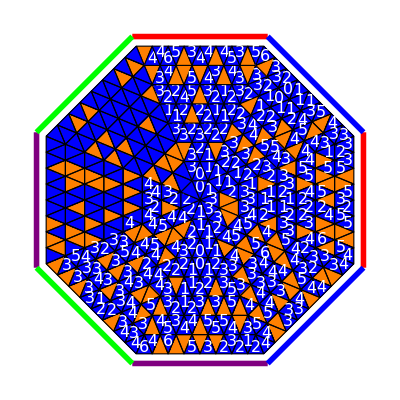

```mathematica
Graphics@displayBoard[board]
```

```mathematica
(*Graphics for each tile. checks if mine and if revealed and based off of that, you have text and color*)
graphicsAtTile[board_,sector_,row_,column_]:=Module[
	{tile = board⟦sector,row,column⟧},
		{
		EdgeForm[{Thickness[Large],Black}],{colorAtTile[board,sector,row,column],Triangle[tile⟦TRIPOINTI⟧]},
		If[tile⟦REVEALORNOT⟧==REVEALED,Text[Style[tile⟦NMINESI⟧,FontSize->16,FontColor->White],triangleCentroid[tile⟦TRIPOINTI⟧]],Text["",triangleCentroid[tile⟦TRIPOINTI⟧]]]
		}
]
```

```mathematica
colorAtTile[board_,sector_,row_,column_]:= Module[
{tile = board⟦sector,row,column⟧},
	If[tile⟦REVEALORNOT⟧==REVEALED,
		If[tile⟦MINETYPEI⟧ == MINE,
			Return[Red],
			Return[Blue]
		]
		,
		If[tile⟦ISFLAGGEDI⟧ == ISFLAGGED,
			Return[Orange],
			Return[Gray]
		]
	]
]
```

#### Putting it all together

Combine the data for each tile into a single list.

```mathematica
triangleCentroid[triangleCoords_]:=RegionCentroid[Triangle[triangleCoords]]
```

```mathematica
boardSetUp[numOfRows_,numMines_,clickedTile_]:=Module[
{minesData=setupMines[numOfRows,0],
triangleCoords=createBoardSkeleton[numOfRows],
neighborData,
minesOffLimits,
curEqVarMap=1
},
neighborData=setupNeighbors[minesData,triangleCoords];
minesOffLimits=Append[neighborData⟦clickedTile⟦1⟧,clickedTile⟦2⟧,clickedTile⟦3⟧,1⟧,clickedTile];
minesData=setupMines[numOfRows,numMines,minesOffLimits];
neighborData=setupNeighbors[minesData,triangleCoords];
Return[
Table[
Table[
Table[
{minesData⟦sectorI,rowI,tileI⟧,
NOTREVEALED,
neighborData⟦sectorI,rowI,tileI,1⟧,
triangleCoords⟦sectorI,rowI,tileI⟧,
If[minesData⟦sectorI⟧⟦rowI⟧⟦tileI⟧ == 0,neighborData⟦sectorI,rowI,tileI,2⟧,""],
NOTFLAGGED
}
,{tileI,1,Length@minesData⟦sectorI,rowI⟧}
]
,{rowI,1,Length@minesData⟦sectorI⟧}
]
,{sectorI,1,8}
]
]
]
```

### Interaction With Board

```mathematica
SetAttributes[play,HoldAll]
play[board_,boardGraphics_]:=
Row[{DynamicModule[{numOfRows,, factor,c = type ,sector,row,column,clickType = {"Reveal","Flag","Reset"},buttenCount = 0}, 
ClickPane[
	Dynamic[
	(*Display*)
		Graphics[{boardGraphics,displayBoardConnections[board]}, ImageSize->Large]
		],
		(*Interaction*)
	(processClick[sectionLst,board,boardGraphics, #,type])&

	]
	(*Buttons and sliders*)
	],Column[{
	Button[StringForm["Flags Left: `1`",(Dynamic[flag])]],
	Button[StringForm["Revealed Tiles: `1`",Dynamic[count]]],
	Button[Dynamic[type],If[type == "Reveal", type = "Flag",type = "Reveal"]],
	Button["Randomize", flag = 8*factor*numOfRows*numOfRows; board = boardSetUp[numOfRows,flag,{sector,row,column}]; boardGraphics = displayBoard[board];count=0],
	{Slider[Dynamic[numOfRows],{4,10,1}],StringForm["Rows: `1`",Dynamic[numOfRows]]},
	{Slider[Dynamic[factor],{0.1,0.5,0.1}],StringForm["Mine Density: `1`",Dynamic[factor]]},
	{Slider[Dynamic[sector],{1,8,1}],StringForm["Sector Clicked: `1`",Dynamic[sector]]},
	{Slider[Dynamic[row],{1,Dynamic[numOfRows],1}],StringForm["Row Clicked: `1`",Dynamic[row]]},
	{Slider[Dynamic[column],{1,Dynamic[2*numOfRows-1],1}],StringForm["Tile Clicked: `1`",Dynamic[column]]}
	}]}
]
```

```mathematica
SetAttributes[processClick,HoldAll]
processClick[sectionLst_,board_,boardGraphics_,clicked_,flagornot_]:= Module[
	{triangle,revealedTiles},
	(*Getting the location of the tile that was clicked*)
	triangle = triangleAtPoint[clicked⟦1⟧,clicked⟦2⟧];
	If[flagornot== "Flag",
		(*Incrementing and decrementing flag count*)
		If[board⟦triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧,ISFLAGGEDI⟧, flag++, flag--];
		(*changing whether the falgged status of the tile
		Also changing the graphics for it*)
		board⟦triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧,ISFLAGGEDI⟧=!board⟦triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧,ISFLAGGEDI⟧;
		boardGraphics⟦triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧⟧ = graphicsAtTile[board,triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧];
		
		Return[Nothing] 
		,
		If[board⟦triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧,REVEALORNOT⟧==REVEALED,Return[Nothing]];
		revealedTiles = revealTile[board,triangle⟦1⟧,triangle⟦2⟧,triangle⟦3⟧]];
	If[revealedTiles == False,Print["Mine"]; Return[Nothing]];
	count += Length@DeleteDuplicates[revealedTiles];
	AppendTo[sectionLst,DeleteDuplicates[revealedTiles]];
	Do[
		(*Revealing tiles*)
		board⟦tiles⟦1⟧,tiles⟦2⟧,tiles⟦3⟧,REVEALORNOT⟧ = REVEALED;
		boardGraphics⟦tiles⟦1⟧,tiles⟦2⟧,tiles⟦3⟧⟧ = graphicsAtTile[board,tiles⟦1⟧,tiles⟦2⟧,tiles⟦3⟧]; 

	,{tiles,revealedTiles}];
	
	
]
```

```mathematica
SetAttributes[toggleFlag,HoldFirst]
toggleFlag[board_,section_,row_,column_]:= board⟦section,row,column,ISFLAGGEDI⟧ = !board⟦section,row,column,ISFLAGGEDI⟧;
```

```mathematica
SetAttributes[revealTile,HoldAll]
revealTile[board_,sector_,row_,tile_]:=Module[
{tileStack={{sector,row,tile}},
allSectors={},
currentTile},
	If[board⟦sector,row,tile,MINETYPEI⟧==MINE,Return[False]];
	
	(*Standard flood fill stuff*)
	While[Length@tileStack>0,
	(*Pop tile and reveal*)
		currentTile=tileStack⟦Length@tileStack⟧;
		tileStack=Delete[tileStack,Length@tileStack];
		board⟦currentTile⟦1⟧,currentTile⟦2⟧,currentTile⟦3⟧,REVEALORNOT⟧=REVEALED;
		(*Add neighbors to stack*)
		If[board⟦currentTile⟦1⟧,currentTile⟦2⟧,currentTile⟦3⟧,NMINESI⟧==0,
			Do[
				If[
					board⟦neighbor⟦1⟧,neighbor⟦2⟧,neighbor⟦3⟧,REVEALORNOT⟧==NOTREVEALED,
					AppendTo[tileStack,neighbor];
					AppendTo[allSectors,neighbor];
					,
					Nothing
				];
			,{neighbor,board⟦currentTile⟦1⟧,currentTile⟦2⟧,currentTile⟦3⟧,NEIGHBORDATAI⟧}
			]
		];
	];
	AppendTo[allSectors,{sector,row,tile}];
	Return[allSectors]
]
```

```mathematica
(*Helper function tofigure out which sector the point is in*)
whichSector[x_,y_]:=Module[
{curPoint={x,y},θ=π/4},
Do[
If[-Cot[(3π)/8]curPoint⟦2⟧<curPoint⟦1⟧<Cot[(3π)/8]curPoint⟦2⟧,Return[i]];
curPoint={{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.curPoint
,{i,1,8}
]
]
```

```mathematica
(*Helper function to figure out which tile the point is in given the row*)
findTile[row_,point_]:=Module[
{tempPoint=point+{(row-1)*Cos[3π/8],-(row-1)Sin[(3π)/8]},
checkerEq=ArcCos[Cos[(x)(π/Cos[3π/8])]]*Sin[3π/8]/π},
If[tempPoint⟦2⟧<checkerEq/.{x->tempPoint⟦1⟧},(*Pointing up triangle*)
Return[2*Ceiling[tempPoint⟦1⟧/(2Cos[3π/8])]];
,(*Pointing down triangle*)
Return[2*Round[tempPoint⟦1⟧/(2Cos[3π/8])]+1];
]
]
```

```mathematica
triangleAtPoint[x_,y_]:=Module[
{sector=whichSector[x,y],
row,tile,
checkPoint,θ=π/4},
checkPoint={{Cos[(sector-1)θ],-Sin[(sector-1)θ]},{Sin[(sector-1)θ],Cos[(sector-1)θ]}}.{x,y};
row=Ceiling[checkPoint⟦2⟧*Csc[(3π)/8]];
tile=findTile[row,checkPoint];
Return[{sector,row,tile}]
]
```

### Solver

#### Query

```mathematica
(*Global Variables for indexing*)
QUEREVEALTILE=0;
QUETOGGLEFLAG=1;
QUETILETYPE=2;
QUEGETNEIGHBORS=3;
QUERYGRAPHICS=4;
QUERYCOMPLETE=5;
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryReveal[input_]:=revealTile[board,input⟦2⟧,input⟦3⟧,input⟦4⟧]
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryToggleFlag[input_]:=toggleFlag[board,input⟦2⟧,input⟦3⟧,input⟦4⟧]
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryTileType[input_]:=
Which[
board⟦input⟦2⟧,input⟦3⟧,input⟦4⟧,ISFLAGGEDI⟧==ISFLAGGED,{MINE,1},
board⟦input⟦2⟧,input⟦3⟧,input⟦4⟧,REVEALORNOT⟧==REVEALED,{NOTMINE,board⟦input⟦2⟧,input⟦3⟧,input⟦4⟧,NMINESI⟧},
True,-1
]
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryNeighbors[input_]:=board⟦input⟦2⟧,input⟦3⟧,input⟦4⟧,NEIGHBORDATAI⟧
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryGetDisplay[input_]:=displayBoard[board]
```

```mathematica
(*Method to allow solver indirect access to the board*)
queryIsComplete[input_]:=isComplete[board]
```

```mathematica
(*Perform query on board. Can be updated as needed, but it must implement:
* revealTile[] - Needs an input of form {QUEREVEALTILE,sector, row, tile}. Return the output of revealTile[] and perform the operation on the given board
* toggleFlag[] - Needs an input of form {QUETOGGLEFLAG, sector, row, tile}. Turn on or off the flag and don't output anything
* getTile[] - Needs an input of form {QUETILETYPE, sector,row,tile}. Returns a number representing the tile, a -1 being unknown, 0 being revealed, and 1 being a flag.
*)
SetAttributes[queryBoard,HoldFirst]
queryBoard[input_]:=
Switch[input⟦1⟧,
QUEREVEALTILE,
Return[queryReveal[input]],
QUETOGGLEFLAG,
queryToggleFlag[input],
QUETILETYPE,
Return[queryTileType[input]],
QUEGETNEIGHBORS,
Return[queryNeighbors[input]],
QUERYGRAPHICS,
Return[queryGetDisplay[input]],
QUERYCOMPLETE,
Return[queryIsComplete[input]]
]
```

#### HelperFunctions

```mathematica
flattenBoardIndex[index_,numRows_]:=
(*Add sector*)
(index⟦1⟧-1)numRows^2+
(*Add row*)
(index⟦2⟧-1)^2+
(*Add tile*)
index⟦3⟧
```

```mathematica
boardifyFlatIndex[index_,numRows_]:=
Module[
{sector=Ceiling[index/numRows^2],
row=Ceiling[Sqrt[Mod[index-1,(numRows^2)]+1]]},
Return[{sector,row,index-(sector-1)numRows^2-(row-1)^2}]

]
```

#### Equation Solvers

```mathematica
intersectionEqVec[eq1_,eq2_]:=Table[If[eq1⟦varPos⟧==eq2⟦varPos⟧&&eq1⟦varPos⟧==1,1,0],{varPos,Length@eq1-1}]
```

```mathematica
(*Solves a linear system of equations with binary variable values*)
cspSolve[binaryMat_]:=Module[
{binaryMatExtra=binaryMat,
newEqs={},
boolSols={},
varPosLst={},
curIndex=0,
changedSomething=True
},
While[changedSomething,
binaryMatExtra=DeleteDuplicates[binaryMatExtra];
changedSomething=False;
Do[
Do[
(*Bad cases*)
If[binaryMatExtra⟦eq1⟧==eq2||(!MemberQ[TakeDrop[binaryMatExtra⟦eq1⟧,Length@eq2-1]⟦1⟧,1]||!MemberQ[TakeDrop[eq2,Length@eq2-1]⟦1⟧,1]),Continue[]];
(*We can simplify*)
If[Append[intersectionEqVec[binaryMatExtra⟦eq1⟧,eq2],eq2⟦-1⟧]==eq2,
(*Subtract eq2 from eq1*)
binaryMatExtra⟦eq1⟧-=eq2;
changedSomething=True;
(*Get variable positions*)
varPosLst=Table[If[binaryMatExtra⟦eq1,i⟧==1,i,Nothing],{i,Length@binaryMatExtra⟦eq1⟧-1}];
(*All mines*)
If[Length[varPosLst]===binaryMatExtra⟦eq1,-1⟧,
Do[
AppendTo[newEqs,Table[0,{i,Length@eq2}]];
newEqs⟦-1,varPos⟧=1;
newEqs⟦-1,-1⟧=1;
changedSomething=True;
,{varPos,varPosLst}
]
];
(*All not mines*)
If[binaryMatExtra⟦eq1,-1⟧==0,
Do[
AppendTo[newEqs,Table[0,{i,Length@eq2}]];
newEqs⟦-1,varPos⟧=1;
newEqs⟦-1,-1⟧=0;
changedSomething=True;
,{varPos,varPosLst}
]
];
];
,{eq2,binaryMatExtra}
]
,{eq1,Length@binaryMatExtra}
];
(*Add in equations*)
Do[
AppendTo[binaryMatExtra,eq]
,{eq,newEqs}
];
];
binaryMatExtra=DeleteDuplicates[binaryMatExtra];
Return[binaryMatExtra]
]
```

```mathematica
(*Given a reduced linear system of equations in matrix form, returns a list of boolean values for each variable*)
findKnownSolutions[matReduceRes_]:=Module[
{valLst,varPosLst,lhs,rhs,definiteSols=Array[p,Length@matReduceRes⟦1⟧-1]},
Do[
lhs=TakeDrop[eq,Length@eq-1]⟦1⟧;
rhs=TakeDrop[eq,Length@eq-1]⟦2,1⟧;
Which[
(*Cannot glean information case*)
Length@Select[lhs,!(#==1||#==0)&]>0,
Continue[],
(*All mines case*)
Sum[lhs⟦i⟧,{i,Length@lhs}]==rhs,
Do[
If[lhs⟦i⟧==1,definiteSols⟦i⟧=1]
,{i,Length@lhs}
],
(*Revealed case*)
rhs==0,
Do[
If[lhs⟦i⟧==1,definiteSols⟦i⟧=0]
,{i,Length@lhs}
]

]
,{eq,matReduceRes}
];
Return[Table[If[solution===0||solution===1,solution,-1],{solution,definiteSols}]]
]
```

#### Solver Interface

```mathematica
(*
Returns a nested list in board form with each tile being of form {variableindex, knownvalue}.
knownvalue is -1 for unknown by default, but can be 0 or 1.
variableindex is an integer representing the position of this variable in the linear system matrix.
*)
initSolver[numRows_]:=
Module[
{indexMapping=1,
solverData,eqsPerTile,curTileType},
solverData=Table[
Table[
Table[{indexMapping++,Table[0,{i,8(numRows)^2+1}],Table[0,{i,8(numRows)^2+1}]},{tile,2row-1}
],{row,numRows}],{sector,8}
];
Do[
curTileType=queryBoard[{QUETILETYPE,sectorI,rowI,tileI}];
If[curTileType==-1,Continue[]];
createTileEq[solverData,sectorI,rowI,tileI];

,{sectorI,8}
,{rowI,numRows}
,{tileI,2rowI-1}
];
Return[solverData]
]
```

```mathematica
SetAttributes[createTileEq,HoldFirst];
createTileEq[solverData_,sector_,row_,tile_]:=
Module[
{newEq1=Table[0,{i,8(Length@solverData⟦1⟧)^2+1}],
qTileData=queryBoard[{QUETILETYPE,sector,row,tile}],
newEq2=Table[0,{i,8(Length@solverData⟦1⟧)^2+1}]},
If[qTileData==-1,Return[]];
If[
qTileData⟦1⟧==MINE,
(*MINE CASE*)
newEq1⟦flattenBoardIndex[{sector,row,tile},Length@solverData⟦1⟧]⟧=1;
newEq1⟦Length@newEq1⟧=1;
];
If[
qTileData⟦1⟧==NOTMINE,
(*REVEALED CASE*)
newEq1⟦flattenBoardIndex[{sector,row,tile},Length@solverData⟦1⟧]⟧=1;
newEq1⟦Length@newEq1⟧=0;
Do[
newEq2⟦flattenBoardIndex[neighbor,Length@solverData⟦1⟧]⟧=1
,{neighbor,queryBoard[{QUEGETNEIGHBORS,sector,row,tile}]}
];
newEq2⟦Length@newEq2⟧=qTileData⟦2⟧
];
solverData⟦sector,row,tile,2⟧=newEq1;
solverData⟦sector,row,tile,3⟧=newEq2
]
```

```mathematica
(*Analyze tiles in batches rather than as a lump solve*)
analyzeEqsBatches[solverData_,corrPosBatches_]:=
Module[
{batchSols=Table[analyzeEqs[solverData,batch],{batch,corrPosBatches}],
knowns=Table[-1,{i,8(Length@solverData⟦1⟧)^2}]},
(* Compile known values *)
Do[
knowns⟦tile⟧=Max[knowns⟦tile⟧,batchSol⟦tile⟧]
,{tile,Length@knowns}
,{batchSol,batchSols}
];
Return[knowns]
]
```

```mathematica
(*Analyze the given positions by creating equations representing them and solving*)
analyzeEqs[solverData_,corrPos_]:=
Module[
{sysEqs=DeleteCases[DeleteDuplicates[chooseTiles[solverData,corrPos]],Table[0,{i,8(Length@solverData⟦1⟧)^2}]],
reducedSols,eqLHS,eqRHS,lhs1s,curEq=1,neighborType},
If[Length@sysEqs==0,Return[]];
reducedSols=cspSolve[sysEqs];
Return[findKnownSolutions[reducedSols]]
]
```

```mathematica
chooseTiles[solverInterface_,chosenTiles_]:=
Join[
Table[solverInterface⟦tile⟦1⟧,tile⟦2⟧,tile⟦3⟧,2⟧,{tile,chosenTiles}],
Table[solverInterface⟦tile⟦1⟧,tile⟦2⟧,tile⟦3⟧,3⟧,{tile,chosenTiles}],
Join@@Table[If[queryBoard[Prepend[neighbor,QUETILETYPE]]=!=-1,solverInterface⟦neighbor⟦1⟧,neighbor⟦2⟧,neighbor⟦3⟧,2⟧,Nothing],{tile,chosenTiles},{neighbor,queryBoard[{QUEGETNEIGHBORS,tile⟦1⟧,tile⟦2⟧,tile⟦3⟧}]}]
]
```

```mathematica
(*Perform clicks based on the result of analyzeEqs*)
makeClicks[analResult_]:=
Do[
(*Case no changes to make*)
If[analResult⟦index⟧===-1||queryBoard[Prepend[boardifyFlatIndex[index,Sqrt[Length@analResult/8]],QUETILETYPE]]=!=-1,Continue[]] ;
If[analResult⟦index⟧==1,
queryBoard[Prepend[boardifyFlatIndex[index,Sqrt[Length@analResult/8]],QUETOGGLEFLAG]],
If[queryBoard[Prepend[boardifyFlatIndex[index,Sqrt[Length@analResult/8]],QUEREVEALTILE]]==False,Print["You dumb bro"]
]
]
,{index,Length@analResult}
]
```

```mathematica
SetAttributes[interfaceNext,HoldFirst]
interfaceNext[solverInterface_,heuristicFunc_,modBoard_]:=Module[
{(*Call the heuristic function*)
chosenTiles=heuristicFunc[solverInterface],analResult,clickedTiles},
analResult=analyzeEqs[solverInterface,chosenTiles];
If[modBoard,
makeClicks[analResult];
];
solverInterface=initSolver[Length@solverInterface⟦1⟧];
Return[analResult]
]
```

```mathematica
SetAttributes[autoSolve,HoldFirst]
autoSolve[solverInterface_,heuristicFunc_]:=
Module[
{lastAnal=googoo,
newAnal=interfaceNext[solverInterface,heuristicFunc,True],
steps={},
stepNumber=1},
While[lastAnal=!=newAnal,
Print["Step "<>ToString[stepNumber++]];
lastAnal=newAnal;
AppendTo[steps,queryBoard[{QUERYGRAPHICS}]];
newAnal=interfaceNext[solverInterface,heuristicFunc,True]
];
Return[steps]
]
```

```mathematica
(*With guessing*)
autoSolve[solverInterface_,heuristicFunc_,guessHeurFunc_]:=Module[
{lastAnal=googoo,
newAnal=interfaceNext[solverInterface,heuristicFunc,True],
steps={},
stepNumber=1},
While[!queryBoard[{QUERYCOMPLETE}],
Print["Step "<>ToString[stepNumber++]];
lastAnal=newAnal;
AppendTo[steps,queryBoard[{QUERYGRAPHICS}]];
newAnal=interfaceNext[solverInterface,heuristicFunc,True];
If[newAnal==lastAnal,
makeClicks[guessHeurFunc[solverInterface]]
]
];
Return[steps]
]
```

#### Heuristics for Solver Interface

```mathematica
unknownAround[tile_]:=
Module[{hasUnknown=False},
Do[
If[queryBoard[Prepend[neighbor,QUETILETYPE]]==-1,hasUnknown=True]
,{neighbor,queryBoard[{QUEGETNEIGHBORS,tile⟦1⟧,tile⟦2⟧,tile⟦3⟧}]}
];
Return[hasUnknown]
]
```

```mathematica
testHeur[solverInterface_]:=
Module[
{numRows=Length@solverInterface⟦1⟧},
Table[If[
(*It is revealed and there are unknowns around*)unknownAround[boardifyFlatIndex[index,numRows]]&&
(queryBoard[Prepend[boardifyFlatIndex[index,numRows],QUETILETYPE]]=!=-1&&queryBoard[Prepend[boardifyFlatIndex[index,numRows],QUETILETYPE]]⟦1⟧==NOTMINE),boardifyFlatIndex[index,numRows],Nothing],{index,8(numRows)^2}]
]
```

```mathematica
moreEfficientHeur[solverInterface_,tilesToUse_]:=
Module[
{tilesLeftUse=tilesToUse,beginTile=boardifyFlatIndex[RandomInteger[1,8(Length@solverInterface⟦1⟧)^2]],numRows=Length@solverInterface⟦1⟧},
AppendTo[beginTile,RandomInteger[1,2beginTile⟦2⟧-1]];
While[!(unknownAround[beginTile]&&
(queryBoard[Prepend[beginTile,QUETILETYPE]]=!=-1&&queryBoard[Prepend[beginTile,QUETILETYPE]]⟦1⟧==NOTMINE)),
beginTile=boardifyFlatIndex[RandomInteger[1,8(Length@solverInterface⟦1⟧)^2]];
]
]
```

```mathematica
testGuessHeur[solverInterface_]:=boardifyFlatIndex[RandomInteger[{1,8(Length@solverInterface⟦1⟧)^2}]]
```

### Guessing

```mathematica
edgesOfSection[board_,sectionLst_]:= Module[
{edges = {},tileI,sectionI,tile,neighbors,neighbor},

(*Goes through each tile in the section and checks if the tile has an unrevealed neighbor *)
For[sectionI = 1,sectionI ≤ Length@sectionLst,sectionI++,
	For[tileI = 1, tileI ≤ Length[sectionLst⟦sectionI⟧],tileI++,
		tile = sectionLst⟦sectionI,tileI⟧;
		neighbors = board⟦tile⟦1⟧,tile⟦2⟧,tile⟦3⟧,NEIGHBORDATAI⟧;
		For[neighbor = 1, neighbor ≤ Length@neighbors,neighbor++,
			
			If[board⟦neighbors⟦neighbor,1⟧,neighbors⟦neighbor,2⟧,neighbors⟦neighbor,3⟧,REVEALORNOT⟧ == NOTREVEALED,
			AppendTo[edges,tile] Break[]];
		];
		
	]
];
Return[edges]
]
```

```mathematica
edges = edgesOfSection[board,sectionLst];
```

```mathematica
(*In Progress*)
localProbability[edges_]:= Module[{},
prob = {};
For[i  =1,i≤ Length@edges,i++,
tile = edges⟦i⟧;
AppendTo[prob,Select[board⟦tile⟦1⟧,tile⟦2⟧,tile⟦3⟧,NEIGHBORDATAI⟧,board⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,REVEALORNOT⟧ == NOTREVEALED&]];
]
assoc = Association[];
prob = DeleteDuplicates[Flatten[prob,1]];
For[j = 1,j≤ Length@prob,j++,

AssociateTo[assoc,{prob⟦j⟧-> 0}]
];

For[ k =1, k≤ Length@edges, k++,
location = edges⟦k⟧;

tile = board⟦location⟦1⟧,location⟦2⟧,location⟦3⟧,NMINESI⟧;
unRevealedNeighbors = Select[board⟦location⟦1⟧,location⟦2⟧,location⟦3⟧,NEIGHBORDATAI⟧,board⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,REVEALORNOT⟧ == NOTREVEALED&];
numOfNeighbors = Length@unRevealedNeighbors;
For[unRevealedNeighborI = 1,unRevealedNeighborI ≤ numOfNeighbors, unRevealedNeighborI++,
AssociateTo[assoc,unRevealedNeighbors⟦unRevealedNeighborI⟧-> assoc[unRevealedNeighbors⟦unRevealedNeighborI⟧] + NMINESI / numOfNeighbors];
] 
];
Position[assoc,Sort[Values[assoc]]⟦1⟧];
Print[assoc]
]
```